```mathematica
半无限大金属板周围的电场与电势分布
```

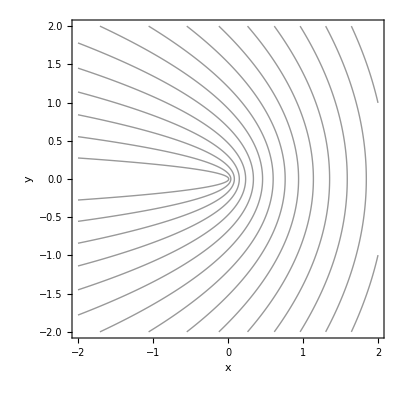

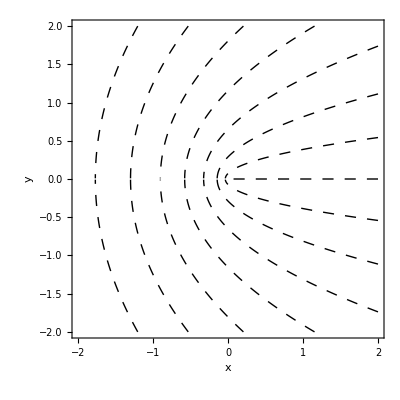

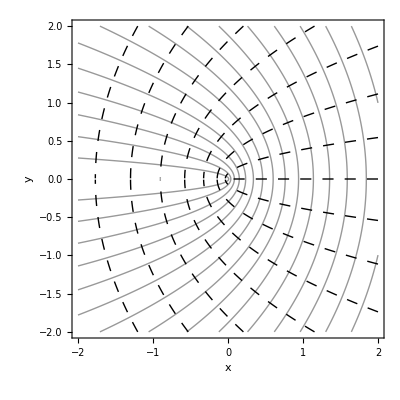

```mathematica
z=x+ⅈ*y;w[z_]:=√z;
real=ComplexExpand[Re[w[z]]];
imaginary=ComplexExpand[Im[w[z]]];
field=ContourPlot[real,{x,-2,2},{y,-2,2},
ContourShading->False,PlotPoints->100,
Contours->15,Axes->True,AxesLabel->{"x","y"}]
potential=ContourPlot[imaginary,{x,-2,2},
{y,-2,2},ContourShading->False,PlotPoints->100,
Contours->15,ContourStyle->Dashing[{0.02,0.02}],
Axes->True,AxesLabel->{"x","y"}]
Show[{potential,field}]
Clear[z,w,real,imaginary,potential,field]
```